## Data for b_n

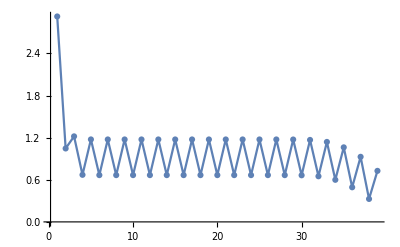

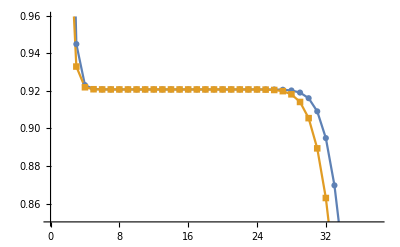

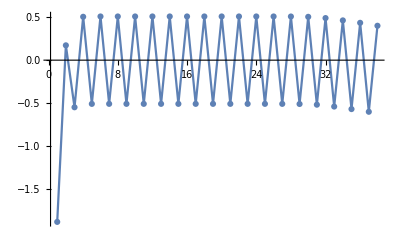

```mathematica
bnFig4 :={2.927468273933625,1.0463987848648626,1.2188417085776668,0.6707967018089253,1.1751838649270259,0.6666321695259654,1.1747818339713372,0.6665930333550208,1.1747779981019844,0.6665926572546431,1.1747779611298323,0.6665926536251924,1.1747779607728601,0.6665926535901151,1.1747779607692814,0.6665926535889046,1.1747779607635715,0.6665926535534124,1.1747779605500306,0.6665926523196478,1.1747779537255645,0.6665926162944564,1.1747777728888742,0.6665917566382809,1.1747739211701012,0.6665755814704747,1.1747106793080622,0.6663472201064781,1.1739566654408662,0.6640969086027491,1.167972425935831,0.650088333453247,1.1395123324354621,0.5998071203034444,1.0622878271074712,0.4931868530022124,0.9274632223084623,0.32716340436325936,0.7272652942473325}(*Jz=0*)
ListPlot[bnFig4, PlotRange -> All, PlotMarkers->Automatic,Joined -> True] 
ListPlot[{MovingAverage[bnFig4,2],MovingAverage[bnFig4,4]},PlotMarkers -> Automatic,Joined -> True ]
ListPlot[Differences[bnFig4],PlotMarkers->Automatic,Joined -> True, PlotRange-> All]
```

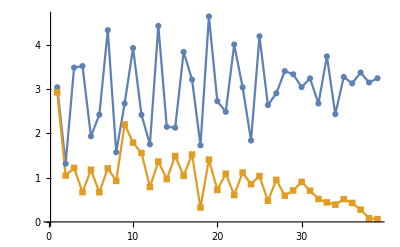

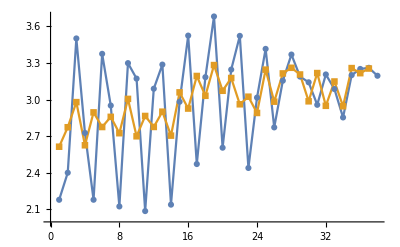

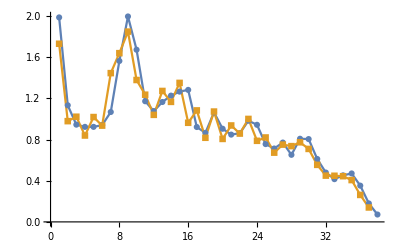

```mathematica
bnFig5a:={3.0400238668417168,1.3144013365513953,3.4844044600820596,3.5193127616405593,1.933104652421285,2.4218774639715557,4.329207613520081,1.5729150515772254,2.672172096412898,3.9264058171800778,2.417748265265686,1.7511766650766432,4.426840652725243,2.1476213068988605,2.126915464815187,3.8372819347748126,3.213085222038835,1.7281579026285283,4.639558626082215,2.725033473098076,2.4847129101490553,4.00709840723251,3.038634342193727,1.8380331509859555,4.193950611329708,2.6381870152084366,2.9047899626042626,3.4052613616772605,3.333945270162092,3.0434514581449954,3.2401153163313237,2.6737794878488654,3.73872369990012,2.4337272075285012,3.2725811579769224,3.1288149196562633,3.3736780652090186,3.14760264002941,3.2432788709919906
} (*Jz =0.001*)
shbnFig5a:= {2.9269023261885776,1.0466212832250963,1.218867903471258,0.6709546154305369,1.175754642825508,0.6709168118158226,1.2093517909386995,0.9261016986580832,2.2007679906555873,1.7911609338488754,1.5543334045667432,0.7902278219843883,1.3631626577688771,0.9666786460828897,1.4866316123998136,1.0448388332014313,1.5201940722867022,0.3235855919093519,1.405986226664078,0.72227399778671,1.0877999441596091,0.6083495641201582,1.1145669553060742,0.8516683062295157,1.034970493666146,0.47689835857439683,0.9489067173618276,0.5926993150805042,0.7108776781541905,0.9047304919440139,0.7046330396526299,0.5178119337415329,0.4403189058209584,0.39037117888037554,0.5138728190865172,0.4276121948003495,0.2771428840640833,0.08137059526299606,0.06208558523021275}(*Jz=0.001*)

ListPlot[{bnFig5a,shbnFig5a}, PlotRange-> All, PlotMarkers -> Automatic,Joined -> True]
ListPlot[{MovingAverage[bnFig5a,2],MovingAverage[bnFig5a,3]},PlotMarkers -> Automatic,Joined -> True ]
ListPlot[{MovingAverage[shbnFig5a,2],MovingAverage[shbnFig5a,3]},PlotMarkers -> Automatic,Joined -> True ]
```

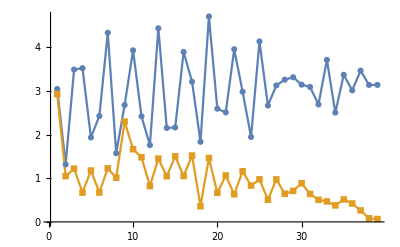

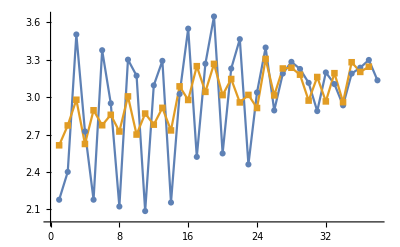

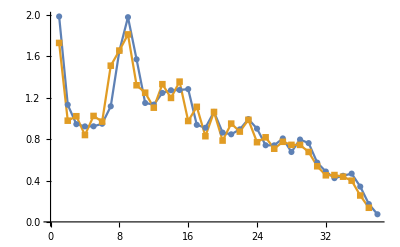

```mathematica
bnFig5b:={3.040236310920305,1.3149152977109135,3.486382465345563,3.5178516909856232,1.9323995335142639,2.4232136901756385,4.328297246150172,1.5724005761148427,2.6742578568473103,3.926361930341372,2.416668516652572,1.756640134527045,4.431896064604524,2.149395880480347,2.160943699776385,3.8889015502562905,3.208870813518093,1.833540030127507,4.7015189686977354,2.591270311689329,2.5060641036465876,3.951067025399871,2.9780590444882162,1.94303380485012,4.131699899090741,2.663269591298808,3.1231994378581156,3.2548188004403023,3.310546865124976,3.1405911151947565,3.0882731504745933,2.687535084501787,3.707827271755516,2.501244140388248,3.366557367806908,3.0102540791202674,3.4616785071181244,3.1340761783420525,3.135125453372681
} (*Jz =0.00125*)
shbnFig5b :={2.926894639548803,1.0466616055107354,1.2188877808489562,0.6710407139353707,1.1760570936071104,0.6730670353455771,1.2251016736114502,1.0110506490371178,2.295698245624344,1.6639848868551108,1.4804144725380735,0.819656305781607,1.448889337536871,1.0454901544079045,1.5011060475863196,1.0501010712779766,1.5183478001058497,0.35855957212610096,1.462238832226098,0.6651573473471467,1.0620588422817243,0.6319793911480973,1.1578419663585615,0.8300766093555837,0.9734434304142764,0.5086581576673415,0.9723684794172155,0.6422577067020522,0.709657761964934,0.8833975481330963,0.6407529225787699,0.5055570709401697,0.46810517250401673,0.3781189615578521,0.5132412280229328,0.4206437560289373,0.262642466976031,0.0826460608336616,0.06469517816484932} 
ListPlot[{bnFig5b,shbnFig5b}, PlotRange-> All,PlotMarkers -> Automatic,Joined -> True]
ListPlot[{MovingAverage[bnFig5b,2],MovingAverage[bnFig5b,3]},PlotMarkers -> Automatic,Joined -> True ]
ListPlot[{MovingAverage[shbnFig5b,2],MovingAverage[shbnFig5b,3]},PlotMarkers -> Automatic,Joined -> True ]
```

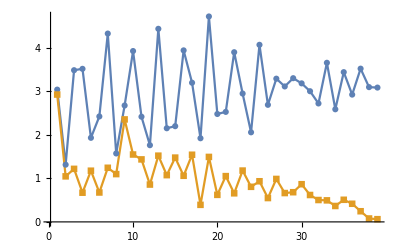

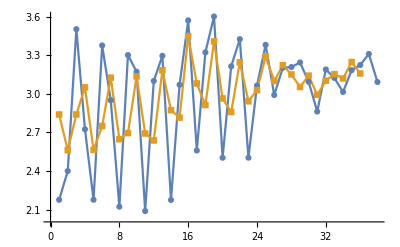

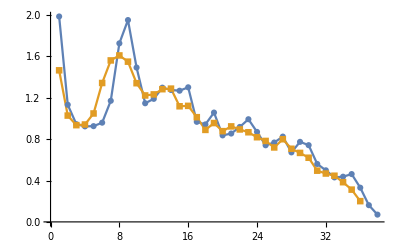

```mathematica
bnFig5c:={3.0402264367712872,1.3149713912539942,3.4863640146364663,3.5178505461445635,1.9324608343771883,2.4233932265680367,4.3282889436487055,1.5726768755339093,2.6753426926219555,3.9268046420507434,2.4170965717007173,1.762717922447203,4.437588146520089,2.1522102701255936,2.1997241619310755,3.94204278171946,3.1982091613519446,1.9222375368368763,4.721412482546072,2.4799263745343474,2.528233149938934,3.8995973459663325,2.94968738610458,2.0587895807054,4.069960146275051,2.6905122655126674,3.2916399899220075,3.1128984877917145,3.3029477216274112,3.1840270171465557,3.0031606604966172,2.7218638117006386,3.65689149140402,2.5880438832249095,3.4416222390040665,2.9255554197179605,3.522017426945721,3.0971139252568167,3.0868901363215637
} (*Jz =0.0015*)
shbnFig5c:= {2.926869695902226,1.046703220292564,1.2189110159913241,0.6711456913700625,1.1764252864278744,0.675672459613351,1.2437201533640194,1.0984792345601802,2.3552935846742864,1.5487771209265957,1.4365323814193511,0.8581397249971742,1.522050038074711,1.0743618489549,1.4774301623623347,1.0599738497249327,1.543359265429532,0.3921295916258166,1.4933242828295645,0.6213861606854143,1.0519789102902777,0.6571967332329931,1.1794397493215631,0.8062150787178358,0.9340139097451843,0.5479408800127556,0.9873779552092504,0.6625976769402924,0.6821264570125983,0.8660605290372163,0.618097334159885,0.5026790659812871,0.49496053415983593,0.3657665353817406,0.5082306924168227,0.4168360767104956,0.24493598615702747,0.07848623347309375,0.062473218756151055}
ListPlot[{bnFig5c,shbnFig5c}, PlotRange-> All, PlotMarkers -> Automatic,Joined -> True]
ListPlot[{MovingAverage[bnFig5c,2],MovingAverage[bnFig5c,4]},PlotMarkers -> Automatic,Joined -> True ]
ListPlot[{MovingAverage[shbnFig5c,2],MovingAverage[shbnFig5c,4]},PlotMarkers -> Automatic,Joined -> True ]
```

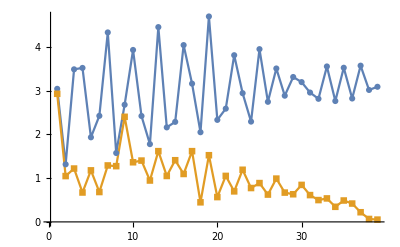

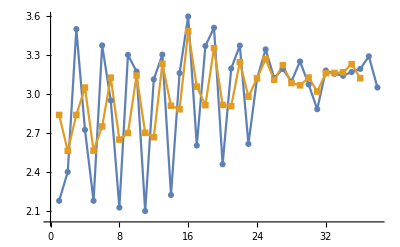

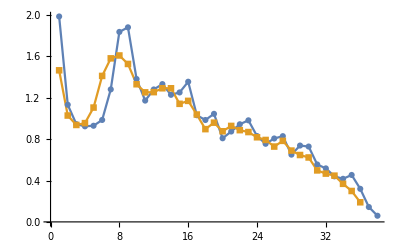

```mathematica
bnFig5d:={3.0401886624548196,1.3150067029962746,3.4856739218966304,3.5177197379728335,1.9324277531074847,2.423018430508106,4.328678347618334,1.573835774644631,2.676706584995272,3.9283085419082147,2.4195518619078653,1.7768675514381775,4.45033905274336,2.1593676715707155,2.285216857907511,4.039230537783231,3.1584813922812685,2.0486146674756793,4.693481944111241,2.330839458709374,2.587131872227865,3.8080795950719746,2.9404987521724912,2.291439073896515,3.9467423396072365,2.7435238155291355,3.5048484330019254,2.8833389805217733,3.31042183915508,3.193643871150016,2.9549609714053005,2.8123604003611313,3.551216604397122,2.7614499587065686,3.5216992246274788,2.819447797491889,3.569385031308959,3.0144022836342272,3.0869868530427254
} (*Jz =0.002*)
shbnFig5d:={2.926793105551294,1.0468026773272618,1.2189692817354973,0.6714131418195206,1.1773684217198976,0.6823425333484557,1.2896668767523365,1.2734622286560573,2.4010349451729844,1.3623669238631442,1.4009341614696977,0.9455101439503106,1.6160385445825833,1.0491264461213174,1.4089040987394503,1.094980544764778,1.616122521082864,0.4473345044971437,1.5233816954695747,0.5667960788890644,1.0508356207341925,0.697532251485352,1.1909714128901232,0.773627723977301,0.886813437672645,0.6241382352145484,0.989057114673953,0.6693952187753436,0.6315307757353418,0.8452547250711744,0.612274121607606,0.4984166137180525,0.5364494791549361,0.3447402905241775,0.4885988239810474,0.41918030156699265,0.22067844285888255,0.0669202864060326,0.052125477356110166}
ListPlot[{bnFig5d,shbnFig5d}, PlotRange-> All, PlotMarkers -> Automatic,Joined -> True]
ListPlot[{MovingAverage[bnFig5d,2],MovingAverage[bnFig5d,4]},PlotMarkers -> Automatic,Joined -> True ]
ListPlot[{MovingAverage[shbnFig5d,2],MovingAverage[shbnFig5d,4]},PlotMarkers -> Automatic,Joined -> True ]
```

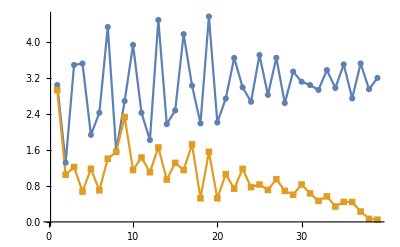

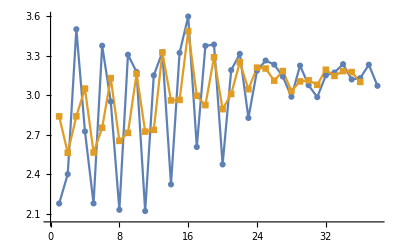

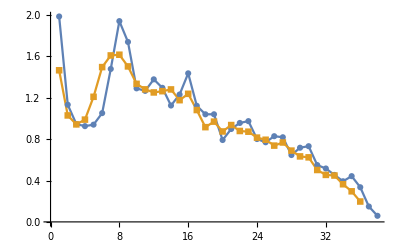

```mathematica
bnFig5e:={3.040115446472635,1.3154129231758869,3.485536813491664,3.517725773067859,1.9328790733669732,2.424297871570192,4.32858718506729,1.5758335221674173,2.684560437014627,3.9314693289435634,2.422490114646216,1.818383857193743,4.483864340822736,2.1713676073835844,2.474234448309732,4.1705662455028945,3.026328033070678,2.1878370919149988,4.5627044026689205,2.2081874080502297,2.7407774324434837,3.641601463911095,2.9875455385348824,2.667732927905821,3.706653353923677,2.8210078198328654,3.64475610431281,2.6396819871973016,3.337910142956728,3.1128478604791123,3.039371568245878,2.9317016352489933,3.370873701857399,2.9748562281373587,3.498144134339986,2.7422590121977284,3.5187565564143064,2.945682151493877,3.197613729666079
} (*Jz =0.003*)
shbnFig5e:={2.9265337222514267,1.0470666856475852,1.2191326973469194,0.672174684151141,1.1800435585982467,0.7008755412822845,1.4033547471230874,1.5549758995851573,2.3286479036920342,1.1521360127309082,1.430868355813469,1.1034686091762684,1.6539203337726895,0.9392181129180829,1.3116705084352764,1.1519622779594914,1.721649550760969,0.523570621912118,1.5575664578146053,0.5240109265443436,1.0598312726456562,0.7372410607192055,1.1766703297970278,0.772295296292034,0.8305550453891483,0.7097830590480729,0.9478145348939283,0.6893806246623334,0.6038801476586845,0.8307709467624101,0.6334523326013322,0.46581211244163784,0.5669973508668561,0.3414636690451314,0.4442302804031425,0.4407892228873207,0.22955919740511654,0.06829007106489711,0.049588186632892745}
ListPlot[{bnFig5e,shbnFig5e}, PlotRange-> All,PlotMarkers -> Automatic, Joined -> True]
ListPlot[{MovingAverage[bnFig5e,2],MovingAverage[bnFig5e,4]},PlotMarkers -> Automatic,Joined -> True ]
ListPlot[{MovingAverage[shbnFig5e,2],MovingAverage[shbnFig5e,4]},PlotMarkers -> Automatic,Joined -> True ]
```

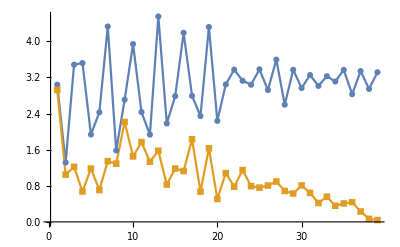

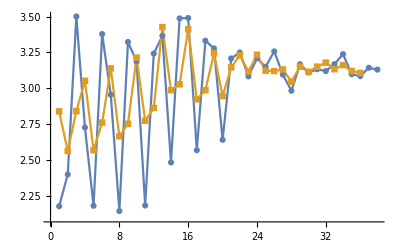

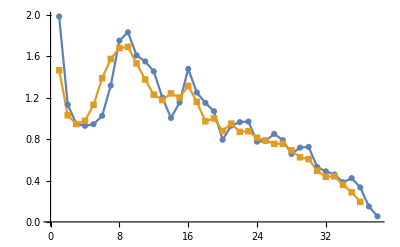

```mathematica
bnFig5f:={3.0397099774010568,1.3162953222853147,3.4832279650581484,3.51883729204806,1.9349694404386957,2.427853475175276,4.329038884348407,1.5822709712353085,2.706311705871136,3.94028291672794,2.432984275306616,1.932973275687832,4.551309021109243,2.180566818191827,2.786117354231376,4.189294784243817,2.79228396421218,2.3449694903528084,4.3188636028315885,2.2377322866511324,3.0445671905593863,3.3726528808704073,3.127204804050611,3.0394472261482663,3.3798327059571402,2.9208628612845455,3.594529486845126,2.59622336236912,3.3702039908665555,2.9663596690558234,3.2536194255597892,3.012737649049821,3.227794869768625,3.1102808320334674,3.366604187145632,2.829968168652571,3.341033392907884,2.945289764228275,3.315519192704578
} (*Jz =0.005*)
shbnFig5f:={2.9242251774143435,1.0471711157997776,1.2194945078623585,0.6740269049352078,1.1829435429425847,0.706078814858769,1.3455272682950465,1.2904517139157947,2.213817390326649,1.4511717029584899,1.7678269842218017,1.3340586611944387,1.5753793050367133,0.8273689033045258,1.1821334209288745,1.1269425137687494,1.8315132096594355,0.6698108157674679,1.6309121663536812,0.5074803614371379,1.0805829564210054,0.7803725724138054,1.1480298629915189,0.791624019158043,0.7594387836474549,0.8065694971152311,0.8951211231891915,0.6850992086064103,0.6288774674321902,0.8078960925051994,0.641626361655161,0.4183290569895045,0.558866469516849,0.35736743600582316,0.40847968776058136,0.4367544879611668,0.23053144787525767,0.06840800770678304,0.03926885661777328}
ListPlot[{bnFig5f,shbnFig5f}, PlotRange-> All, PlotMarkers -> Automatic,Joined -> True]
ListPlot[{MovingAverage[bnFig5f,2],MovingAverage[bnFig5f,4]},PlotMarkers -> Automatic,Joined -> True ]
ListPlot[{MovingAverage[shbnFig5f,2],MovingAverage[shbnFig5f,4]},PlotMarkers -> Automatic,Joined -> True ]
```

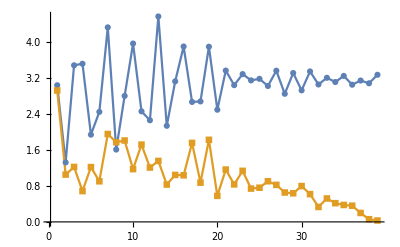

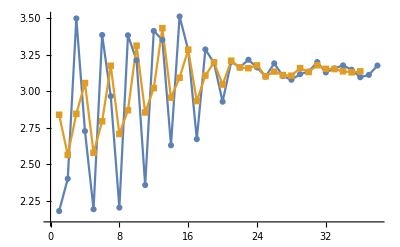

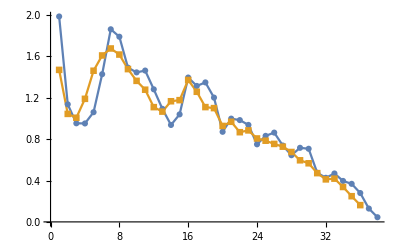

```mathematica
bnFig5g:={3.038935293314955,1.3227165995748098,3.4820221128684943,3.516355170795808,1.9401644339675999,2.4465476212152333,4.3253860965691775,1.6085008366428848,2.801275179431492,3.966115076769445,2.4583515159752265,2.2595517636122073,4.568038487104504,2.1367080610367513,3.12496156979323,3.9004696222307493,2.6672929893501514,2.678838227659358,3.895546168100896,2.4940573955313847,3.3647601457904788,3.040627414533469,3.2866314405661545,3.1468986952194276,3.1809291670801274,3.0217746820552027,3.3619793192539764,2.848239781420664,3.3103614427437766,2.9251432910568633,3.3459776809620774,3.05540283151323,3.204269809298072,3.110275280239013,3.246002760939554,3.0502899831700048,3.143380846244266,3.0823572124614187,3.2712038737966096
} (*Jz =0.01*)
shbnFig5g:={2.921827766239532,1.051836505536722,1.2220044171286981,0.6850999924388047,1.2189540438237452,0.9027251692926486,1.95420415290225,1.7715572138196072,1.8100938044179147,1.173184306860665,1.7186890793229324,1.2085022335461826,1.3558392906218015,0.8307051751086069,1.0442248831005907,1.0354102430522016,1.7567538437131605,0.8729652922997204,1.8251413880304266,0.5791084234266403,1.1635960916453263,0.8337874739707676,1.1352395813352503,0.7404658495505553,0.7602838241681988,0.9038567163728572,0.8232273989544678,0.6534246891275567,0.6364135923996243,0.7968714847941287,0.6176918999040248,0.33198637056703456,0.5207842933289589,0.4158767159111095,0.3763462416107274,0.3599406589453516,0.1985750083658023,0.05945468523440056,0.030758171756832684}
ListPlot[{bnFig5g,shbnFig5g}, PlotRange-> All,PlotMarkers -> Automatic, Joined -> True]
ListPlot[{MovingAverage[bnFig5g,2],MovingAverage[bnFig5g,4]},PlotMarkers -> Automatic,Joined -> True ]
ListPlot[{MovingAverage[shbnFig5g,2],MovingAverage[shbnFig5g,4]},PlotMarkers -> Automatic,Joined -> True ]
```

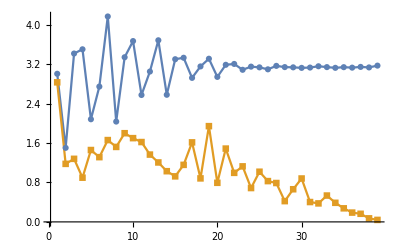

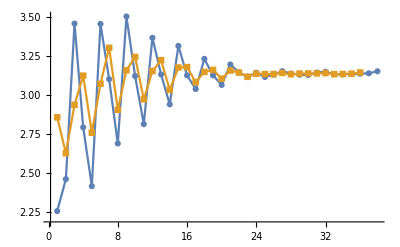

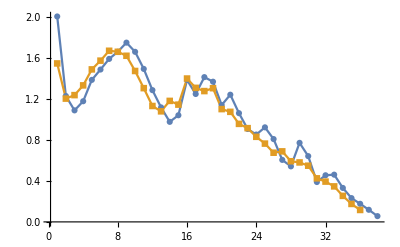

```mathematica
bnFig5h:={3.005237429491079,1.5020992264753432,3.4160416391313,3.5019976327485294,2.0823992720090425,2.7453788506950194,4.16803132486098,2.0354098195634,3.340590865395758,3.668968864737812,2.5745790329885594,3.0505962179938337,3.684868661590578,2.579187962706633,3.3004789525039775,3.330260141997971,2.922071402605289,3.1540835239604417,3.3104228040130024,2.941744767248336,3.1873340956199185,3.204769701738966,3.086026971830903,3.1500681985691337,3.1353044088594437,3.0955568548824495,3.1654182865335145,3.140679575362236,3.135679806065823,3.125031623739224,3.1312414141414013,3.157626133585652,3.1404793382746212,3.125892272381895,3.139064846055145,3.1295891809745013,3.14451440977356,3.1340422443134814,3.170679338148579
} (*Jz =0.05*)
shbnFig5h:={2.831897673175373,1.1773775216792923,1.2794395780527548,0.8968604071564324,1.45802332907109,1.3136017350217288,1.6599604278371192,1.521051431459381,1.7994805030163967,1.699169338682794,1.6199432794033162,1.365641743640742,1.2059317726912042,1.0285746825895625,0.9240126884509955,1.157065644713196,1.6134826233640525,0.8826751902497755,1.9426463069820252,0.7930825241334756,1.4873598429260537,0.9950402860883564,1.1267681257334625,0.6866646122036533,1.0177504422167378,0.8276966022755027,0.7889324455959768,0.4213006931363958,0.6623559554442813,0.8804781186677664,0.40286378419964997,0.3754007363665604,0.5346792155713336,0.3872685127440036,0.27549831814203085,0.18868623325373352,0.1643126283885034,0.07216374548882216,0.04042981746776664}
ListPlot[{bnFig5h,shbnFig5h}, PlotRange-> All, PlotMarkers -> Automatic,Joined -> True]
ListPlot[{MovingAverage[bnFig5h,2],MovingAverage[bnFig5h,4]},PlotMarkers -> Automatic,Joined -> True , PlotRange-> All]
ListPlot[{MovingAverage[shbnFig5h,2],MovingAverage[shbnFig5h,4]},PlotMarkers -> Automatic,Joined -> True , PlotRange-> All]
```

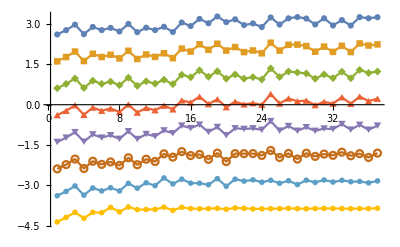

```mathematica
m:=3(*moving average over m sites*)
ListPlot[{MovingAverage[bnFig5a,m],-1.0+ MovingAverage[bnFig5b,m],-2.0+MovingAverage[bnFig5c,m],-3.0+ MovingAverage[bnFig5d,m],-4.0+MovingAverage[bnFig5e,m],-5.0+MovingAverage[bnFig5f,m],-6.0+ MovingAverage[bnFig5g,m],-7.0+ MovingAverage[bnFig5h,m]},PlotMarkers -> Automatic,Joined -> True , PlotRange-> All]
```

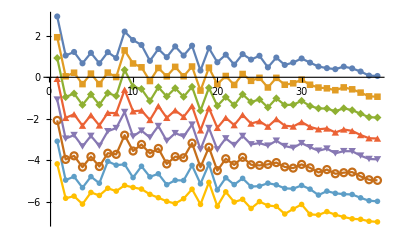

```mathematica
m:=1(*moving average over m sites*)
ListPlot[{MovingAverage[shbnFig5a,m],-1.0+ MovingAverage[shbnFig5b,m],-2.0+MovingAverage[shbnFig5c,m],-3.0+ MovingAverage[shbnFig5d,m],-4.0+MovingAverage[shbnFig5e,m],-5.0+MovingAverage[shbnFig5f,m],-6.0+ MovingAverage[shbnFig5g,m],-7.0+ MovingAverage[shbnFig5h,m]},PlotMarkers -> Automatic,Joined -> True , PlotRange-> All]
```

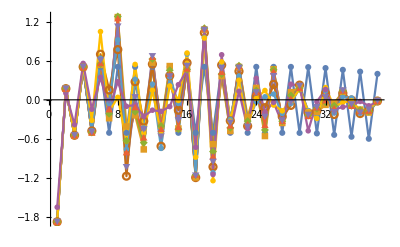

```mathematica
ListPlot[{Differences[bnFig4],Differences[shbnFig5a],Differences[shbnFig5b],Differences[shbnFig5c],Differences[shbnFig5d],Differences[shbnFig5e],Differences[shbnFig5f],Differences[shbnFig5g],Differences[shbnFig5h]}, PlotMarkers -> Automatic,Joined -> True , PlotRange-> All]
```

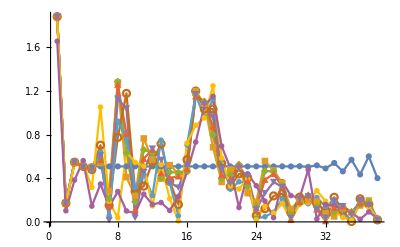

```mathematica
ListPlot[{Abs[Differences[bnFig4]],Abs[Differences[shbnFig5a]],Abs[Differences[shbnFig5b]],Abs[Differences[shbnFig5c]],Abs[Differences[shbnFig5d]],Abs[Differences[shbnFig5e]],Abs[Differences[shbnFig5f]],Abs[Differences[shbnFig5g]],Abs[Differences[shbnFig5h]]}, PlotMarkers -> Automatic,Joined -> True , PlotRange-> All]
```

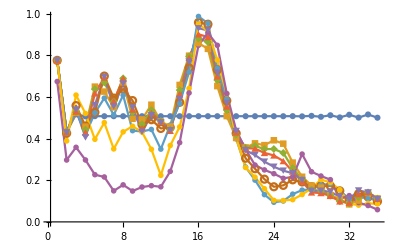

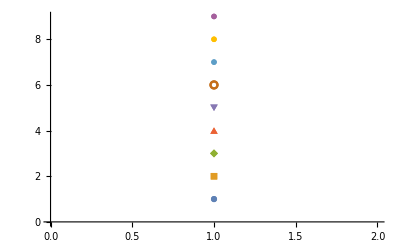

```mathematica
m:=4
ListPlot[{MovingAverage[Abs[Differences[bnFig4]],m],MovingAverage[Abs[Differences[shbnFig5a]],m],MovingAverage[Abs[Differences[shbnFig5b]],m],MovingAverage[Abs[Differences[shbnFig5c]],m],MovingAverage[Abs[Differences[shbnFig5d]],m],MovingAverage[Abs[Differences[shbnFig5e]],m],MovingAverage[Abs[Differences[shbnFig5f]],m],MovingAverage[Abs[Differences[shbnFig5g]],m],MovingAverage[Abs[Differences[shbnFig5h]],m]}, PlotMarkers -> Automatic,Joined -> True , PlotRange-> All]
ListPlot[{{1},{2},{3},{4},{5},{6},{7},{8},{9}}, PlotMarkers -> Automatic,Joined -> True , PlotRange-> All]
```

{0.77631,0.432449,0.523997,0.457831,0.650297,0.62649,0.551088,0.671302,0.495869,0.492588,0.563369,0.482791,0.458396,0.658427,0.799039,0.859519,0.832062,0.652772,0.508726,0.403523,0.357967,0.377623,0.36907,0.392398,0.376117,0.285062,0.217084,0.174737,0.164566,0.12859,0.109441,0.0843008,0.102545,0.139001,0.112947}

{0.392398,0.350493,0.319522,0.26511,0.168874,0.0944724,0.103456,0.231884}

{{1000.,0.392398},{800.,0.350493},{666.667,0.319522},{500.,0.26511},{333.333,0.168874},{200.,0.0944724},{100.,0.103456},{20.,0.231884}}

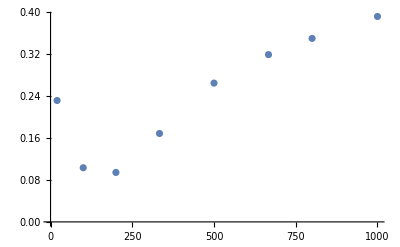

```mathematica
Abs[MovingAverage[Abs[Differences[shbnFig5a]],m]]
X:=24
M= {Abs[MovingAverage[Abs[Differences[shbnFig5a]],m]][[X]],Abs[MovingAverage[Abs[Differences[shbnFig5b]],m]][[X]],MovingAverage[Abs[Differences[shbnFig5c]],m][[X]],MovingAverage[Abs[Differences[shbnFig5d]],m][[X]],MovingAverage[Abs[Differences[shbnFig5e]],m][[X]],MovingAverage[Abs[Differences[shbnFig5f]],m][[X]],MovingAverage[Abs[Differences[shbnFig5g]],m][[X]],MovingAverage[Abs[Differences[shbnFig5h]],m][[X]]}
Jz :={0.001,0.00125,0.0015,0.002,0.003,0.005,0.01,0.05}
data= Transpose@{1/Jz,M}
ListPlot[data]
```

```mathematica
MovingAverage[bnFig4,39]
MovingAverage[bnFig5a,39]
MovingAverage[bnFig5b,39]
MovingAverage[bnFig5c,39]
MovingAverage[bnFig5d,39]
MovingAverage[bnFig5e,39]
MovingAverage[bnFig5f,39]
MovingAverage[bnFig5g,39]
MovingAverage[bnFig5h,39]
```

{0.945971}

{2.98378}

{2.98592}

{2.98931}

{2.99705}

{3.00723}

{3.02207}

{3.04175}

{3.07727}

```mathematica
MovingAverage[bnFig4,39]
MovingAverage[shbnFig5a,39]
MovingAverage[shbnFig5b,39]
MovingAverage[shbnFig5c,39]
MovingAverage[shbnFig5d,39]
MovingAverage[shbnFig5e,39]
MovingAverage[shbnFig5f,39]
MovingAverage[shbnFig5g,39]
MovingAverage[shbnFig5h,39]
```

{0.945971}

{0.942615}

{0.94786}

{0.95149}

{0.956869}

{0.966699}

{0.975681}

{0.981985}

{1.01296}

```mathematica
Differences[{a,b,c,d,e}]
```

{-a+b,-b+c,-c+d,-d+e}

## SSH Hamiltonian

```mathematica
Ham[s_]:=Module[{s1},s1=Table[{n,n+1}->s[[n]],{n,1,Length[s]}];s1=AppendTo[s1,{Length[s]+1,Length[s]+1}->0];s1=SparseArray[s1];s1=s1+Transpose[s1]];
Eigen[s_]:=Sort[Mod[Eigenvalues[Ham[s]],2π,-π]];
```

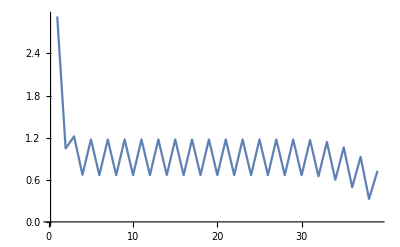

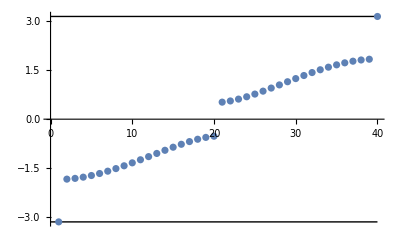

```mathematica
q=bnFig4;
ListPlot[q, PlotRange -> All, Joined -> True] 
Show[Plot[{π,-π},{x,0,40},PlotStyle->{{Black,Thin},{Black,Thin}}],ListPlot[Eigen[q]]]
Min[Abs[Eigen[q]-π],Abs[Eigen[q]π]]
```

```mathematica
Eigen[q]
```

{-3.14121,-1.8336,-1.81063,-1.77335,-1.72315,-1.66162,-1.59047,-1.51136,-1.42585,-1.33541,-1.24141,-1.14518,-1.04807,-0.951556,-0.857377,-0.767682,-0.685243,-0.613645,-0.557273,-0.520837,0.520837,0.557273,0.613645,0.685243,0.767682,0.857377,0.951556,1.04807,1.14518,1.24141,1.33541,1.42585,1.51136,1.59047,1.66162,1.72315,1.77335,1.81063,1.8336,3.14121}

```mathematica
MatrixForm[Chop[MatrixExp[ⅈ Ham[bnFig5a]]]]
```

(-0.785906 | 0.-0.000143492 ⅈ | -0.199466 | 0.-0.214646 ⅈ | 0.465239 | 0.+0.256399 ⅈ | -0.0916577 | 0.-0.0747977 ⅈ | 0.0166781 | 0.+0.00497455 ⅈ | -0.00215569 | 0.-0.00052398 ⅈ | 0.0000748413 | 0.+0.000027288 ⅈ | -4.43333×10^-6 | 0.-6.33883×10^-7 ⅈ | 1.55751×10^-7 | 0.+3.08126×10^-8 ⅈ | -2.92309×10^-9 | 0.-7.33466×10^-10 ⅈ | 1.02707×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.-0.000143492 ⅈ | -0.872149 | 0.-0.246085 ⅈ | 0.309965 | 0.-0.0854471 ⅈ | 0.222818 | 0.+0.0977465 ⅈ | -0.121898 | 0.-0.0343279 ⅈ | 0.0118758 | 0.+0.00600827 ⅈ | -0.00167132 | 0.-0.000262097 ⅈ | 0.000105851 | 0.+0.0000188341 ⅈ | -2.90513×10^-6 | 0.-7.67555×10^-7 ⅈ | 1.62956×10^-7 | 0.+1.63966×10^-8 ⅈ | -4.36903×10^-9 | 0.-6.47496×10^-10 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.199466 | 0.-0.246085 ⅈ | 0.410888 | 0.-0.384695 ⅈ | 0.0816003 | 0.-0.538577 ⅈ | 0.221058 | 0.+0.453862 ⅈ | -0.160303 | 0.-0.0633459 ⅈ | 0.0373871 | 0.+0.0119145 ⅈ | -0.0020433 | 0.-0.000915071 ⅈ | 0.000178504 | 0.+0.0000297019 ⅈ | -8.44315×10^-6 | 0.-1.92601×10^-6 ⅈ | 2.05591×10^-7 | 0.+5.82305×10^-8 ⅈ | -9.14243×10^-9 | 0.-1.20414×10^-9 ⅈ | 2.46869×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.-0.214646 ⅈ | 0.309965 | 0.-0.384695 ⅈ | 0.37638 | 0.-0.655112 ⅈ | 0.114868 | 0.+0.152685 ⅈ | 0.248274 | 0.+0.16925 ⅈ | -0.0852857 | 0.-0.0653807 ⅈ | 0.0255456 | 0.+0.00492422 ⅈ | -0.00252586 | 0.-0.00055298 ⅈ | 0.000100758 | 0.+0.0000312235 ⅈ | -7.74521×10^-6 | 0.-8.83894×10^-7 ⅈ | 2.68247×10^-7 | 0.+4.49257×10^-8 ⅈ | -6.26606×10^-9 | 0.-1.35852×10^-9 ⅈ | 2.14502×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.465239 | 0.-0.0854471 ⅈ | 0.0816003 | 0.-0.655112 ⅈ | 0.358684 | 0.+0.278465 ⅈ | 0.165591 | 0.-0.185893 ⅈ | 0.204919 | 0.+0.118284 ⅈ | -0.114618 | 0.-0.0542622 ⅈ | 0.0115571 | 0.+0.00676258 ⅈ | -0.00165722 | 0.-0.000329559 ⅈ | 0.00011115 | 0.+0.0000299795 ⅈ | -3.6532×10^-6 | 0.-1.18812×10^-6 ⅈ | 2.12334×10^-7 | 0.+3.13639×10^-8 ⅈ | -7.19377×10^-9 | 0.-1.19968×10^-9 ⅈ | 1.10698×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.+0.256399 ⅈ | 0.222818 | 0.-0.538577 ⅈ | 0.114868 | 0.+0.278465 ⅈ | 0.357022 | 0.-0.345408 ⅈ | 0.0855865 | 0.-0.295879 ⅈ | 0.205727 | 0.+0.291413 ⅈ | -0.179391 | 0.-0.0426339 ⅈ | 0.0292232 | 0.+0.00815715 ⅈ | -0.00178617 | 0.-0.000661201 ⅈ | 0.000195581 | 0.+0.0000255587 ⅈ | -8.95693×10^-6 | 0.-1.71632×10^-6 ⅈ | 2.69419×10^-7 | 0.+6.56012×10^-8 ⅈ | -1.15931×10^-8 | 0.-1.12572×10^-9 ⅈ | 2.43075×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.0916577 | 0.+0.0977465 ⅈ | 0.221058 | 0.+0.152685 ⅈ | 0.165591 | 0.-0.345408 ⅈ | 0.377839 | 0.-0.661216 ⅈ | 0.11901 | 0.+0.051577 ⅈ | 0.245931 | 0.+0.303401 ⅈ | -0.0855202 | 0.-0.0760929 ⅈ | 0.0256681 | 0.+0.00637911 ⅈ | -0.00265929 | 0.-0.000882902 ⅈ | 0.000125316 | 0.+0.0000479796 ⅈ | -9.97117×10^-6 | 0.-1.67735×10^-6 ⅈ | 4.36962×10^-7 | 0.+8.24105×10^-8 ⅈ | -8.46577×10^-9 | 0.-1.9335×10^-9 ⅈ | 2.61984×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.-0.0747977 ⅈ | -0.121898 | 0.+0.453862 ⅈ | 0.248274 | 0.-0.185893 ⅈ | 0.0855865 | 0.-0.661216 ⅈ | 0.373199 | 0.-0.042879 ⅈ | 0.181417 | 0.+0.0531948 ⅈ | 0.203109 | 0.+0.068768 ⅈ | -0.0910638 | 0.-0.0391772 ⅈ | 0.0112527 | 0.+0.00536887 ⅈ | -0.00203308 | 0.-0.000315321 ⅈ | 0.000133034 | 0.+0.0000301984 ⅈ | -5.46914×10^-6 | 0.-1.5314×10^-6 ⅈ | 3.09591×10^-7 | 0.+3.37453×10^-8 ⅈ | -8.1776×10^-9 | 0.-1.17099×10^-9 ⅈ | 1.73559×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0166781 | 0.-0.0343279 ⅈ | -0.160303 | 0.+0.16925 ⅈ | 0.204919 | 0.-0.295879 ⅈ | 0.11901 | 0.-0.042879 ⅈ | 0.353846 | 0.-0.0820155 ⅈ | 0.0881794 | 0.-0.676736 ⅈ | 0.205217 | 0.+0.349484 ⅈ | -0.179768 | 0.-0.0574356 ⅈ | 0.0306182 | 0.+0.0130509 ⅈ | -0.00218625 | 0.-0.00100983 ⅈ | 0.000249283 | 0.+0.0000484193 ⅈ | -0.0000145376 | 0.-3.14583×10^-6 ⅈ | 3.63269×10^-7 | 0.+9.33346×10^-8 ⅈ | -1.41165×10^-8 | 0.-2.20191×10^-9 ⅈ | 3.82309×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.+0.00497455 ⅈ | 0.0118758 | 0.-0.0633459 ⅈ | -0.0852857 | 0.+0.118284 ⅈ | 0.205727 | 0.+0.051577 ⅈ | 0.181417 | 0.-0.0820155 ⅈ | 0.376627 | 0.-0.764125 ⅈ | 0.0947148 | 0.+0.0950018 ⅈ | 0.249096 | 0.+0.258225 ⅈ | -0.105741 | 0.-0.069946 ⅈ | 0.0365989 | 0.+0.00687264 ⅈ | -0.00361998 | 0.-0.00100256 ⅈ | 0.000213215 | 0.+0.0000699321 ⅈ | -0.0000164636 | 0.-2.03721×10^-6 ⅈ | 5.61025×10^-7 | 0.+9.04433×10^-8 ⅈ | -1.49604×10^-8 | 0.-2.74548×10^-9 ⅈ | 4.69658×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.00215569 | 0.+0.00600827 ⅈ | 0.0373871 | 0.-0.0653807 ⅈ | -0.114618 | 0.+0.291413 ⅈ | 0.245931 | 0.+0.0531948 ⅈ | 0.0881794 | 0.-0.764125 ⅈ | 0.374937 | 0.+0.0324106 ⅈ | 0.183423 | 0.+0.0105045 ⅈ | 0.201311 | 0.+0.11061 ⅈ | -0.094229 | 0.-0.0630958 ⅈ | 0.013319 | 0.+0.00811236 ⅈ | -0.00254709 | 0.-0.000596022 ⅈ | 0.000214749 | 0.+0.0000553075 ⅈ | -7.35494×10^-6 | 0.-2.17877×10^-6 ⅈ | 3.75497×10^-7 | 0.+6.60282×10^-8 ⅈ | -1.28361×10^-8 | 0.-2.31957×10^-9 ⅈ | 3.61325×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.-0.00052398 ⅈ | -0.00167132 | 0.+0.0119145 ⅈ | 0.0255456 | 0.-0.0542622 ⅈ | -0.179391 | 0.+0.303401 ⅈ | 0.203109 | 0.-0.676736 ⅈ | 0.0947148 | 0.+0.0324106 ⅈ | 0.353974 | 0.-0.111574 ⅈ | 0.110133 | 0.-0.31272 ⅈ | 0.199265 | 0.+0.205292 ⅈ | -0.175143 | 0.-0.0406934 ⅈ | 0.0285666 | 0.+0.010159 ⅈ | -0.00260798 | 0.-0.00103189 ⅈ | 0.000291043 | 0.+0.0000415752 ⅈ | -0.0000132596 | 0.-2.44497×10^-6 ⅈ | 4.57355×10^-7 | 0.+9.42571×10^-8 ⅈ | -1.80082×10^-8 | 0.-2.95585×10^-9 ⅈ | 4.93468×10^-10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0000748413 | 0.-0.000262097 ⅈ | -0.0020433 | 0.+0.00492422 ⅈ | 0.0115571 | 0.-0.0426339 ⅈ | -0.0855202 | 0.+0.068768 ⅈ | 0.205217 | 0.+0.0950018 ⅈ | 0.183423 | 0.-0.111574 ⅈ | 0.379141 | 0.-0.680069 ⅈ | 0.0991473 | 0.-0.0826831 ⅈ | 0.245384 | 0.+0.423627 ⅈ | -0.115545 | 0.-0.103205 ⅈ | 0.0442691 | 0.+0.0128762 ⅈ | -0.00575913 | 0.-0.00182325 ⅈ | 0.000283877 | 0.+0.0000988944 ⅈ | -0.0000197357 | 0.-3.96351×10^-6 ⅈ | 8.72791×10^-7 | 0.+1.77515×10^-7 ⅈ | -3.0883×10^-8 | 0.-5.45112×10^-9 ⅈ | 7.39473×10^-10 | 0.+1.35777×10^-10 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0.+0.000027288 ⅈ | 0.000105851 | 0.-0.000915071 ⅈ | -0.00252586 | 0.+0.00676258 ⅈ | 0.0292232 | 0.-0.0760929 ⅈ | -0.0910638 | 0.+0.349484 ⅈ | 0.249096 | 0.+0.0105045 ⅈ | 0.110133 | 0.-0.680069 ⅈ | 0.383675 | 0.-0.245946 ⅈ | 0.181514 | 0.+0.154595 ⅈ | 0.202281 | 0.+0.0733101 ⅈ | -0.105147 | 0.-0.0603213 ⅈ | 0.0206661 | 0.+0.010812 ⅈ | -0.0039504 | 0.-0.000679771 ⅈ | 0.000262426 | 0.+0.0000573028 ⅈ | -0.0000124597 | 0.-2.95245×10^-6 ⅈ | 6.43208×10^-7 | 0.+1.19221×10^-7 ⅈ | -2.23526×10^-8 | 0.-3.20293×10^-9 ⅈ | 6.20512×10^-10 | 0 | 0 | 0 | 0 | 0 | 0
-4.43333×10^-6 | 0.+0.0000188341 ⅈ | 0.000178504 | 0.-0.00055298 ⅈ | -0.00165722 | 0.+0.00815715 ⅈ | 0.0256681 | 0.-0.0391772 ⅈ | -0.179768 | 0.+0.258225 ⅈ | 0.201311 | 0.-0.31272 ⅈ | 0.0991473 | 0.-0.245946 ⅈ | 0.359069 | 0.+0.203083 ⅈ | 0.121154 | 0.-0.582929 ⅈ | 0.173791 | 0.+0.294567 ⅈ | -0.200758 | 0.-0.0761573 ⅈ | 0.0448413 | 0.+0.0184741 ⅈ | -0.00345361 | 0.-0.00146094 ⅈ | 0.000346199 | 0.+0.0000809941 ⅈ | -0.0000205565 | 0.-4.78031×10^-6 ⅈ | 9.41443×10^-7 | 0.+1.87117×10^-7 ⅈ | -2.8273×10^-8 | 0.-5.77248×10^-9 ⅈ | 7.17694×10^-10 | 0.+1.14289×10^-10 ⅈ | 0 | 0 | 0 | 0
0.-6.33883×10^-7 ⅈ | -2.90513×10^-6 | 0.+0.0000297019 ⅈ | 0.000100758 | 0.-0.000329559 ⅈ | -0.00178617 | 0.+0.00637911 ⅈ | 0.0112527 | 0.-0.0574356 ⅈ | -0.105741 | 0.+0.11061 ⅈ | 0.199265 | 0.-0.0826831 ⅈ | 0.181514 | 0.+0.203083 ⅈ | 0.394368 | 0.-0.670325 ⅈ | 0.119983 | 0.+0.0948921 ⅈ | 0.228057 | 0.+0.349343 ⅈ | -0.170917 | 0.-0.128004 ⅈ | 0.0650672 | 0.+0.0137706 ⅈ | -0.00664554 | 0.-0.00175936 ⅈ | 0.000452483 | 0.+0.000125162 ⅈ | -0.0000315248 | 0.-6.67558×10^-6 ⅈ | 1.42121×10^-6 | 0.+2.28315×10^-7 ⅈ | -4.9504×10^-8 | 0.-6.50352×10^-9 ⅈ | 1.09124×10^-9 | 0.+1.6577×10^-10 ⅈ | 0 | 0 | 0
1.55751×10^-7 | 0.-7.67555×10^-7 ⅈ | -8.44315×10^-6 | 0.+0.0000312235 ⅈ | 0.00011115 | 0.-0.000661201 ⅈ | -0.00265929 | 0.+0.00536887 ⅈ | 0.0306182 | 0.-0.069946 ⅈ | -0.094229 | 0.+0.205292 ⅈ | 0.245384 | 0.+0.154595 ⅈ | 0.121154 | 0.-0.670325 ⅈ | 0.427681 | 0.-0.195447 ⅈ | 0.233445 | 0.+0.199545 ⅈ | 0.162557 | 0.+0.13475 ⅈ | -0.15181 | 0.-0.105007 ⅈ | 0.0258178 | 0.+0.0146507 ⅈ | -0.00441827 | 0.-0.00126565 ⅈ | 0.000385544 | 0.+0.0001061 ⅈ | -0.0000243249 | 0.-5.58134×10^-6 ⅈ | 9.57723×10^-7 | 0.+2.21526×10^-7 ⅈ | -3.08642×10^-8 | 0.-5.47463×10^-9 ⅈ | 8.76115×10^-10 | 0.+1.44146×10^-10 ⅈ | 0 | 0
0.+3.08126×10^-8 ⅈ | 1.62956×10^-7 | 0.-1.92601×10^-6 ⅈ | -7.74521×10^-6 | 0.+0.0000299795 ⅈ | 0.000195581 | 0.-0.000882902 ⅈ | -0.00203308 | 0.+0.0130509 ⅈ | 0.0365989 | 0.-0.0630958 ⅈ | -0.175143 | 0.+0.423627 ⅈ | 0.202281 | 0.-0.582929 ⅈ | 0.119983 | 0.-0.195447 ⅈ | 0.409947 | 0.+0.069687 ⅈ | 0.20259 | 0.-0.143771 ⅈ | 0.140502 | 0.+0.221615 ⅈ | -0.206506 | 0.-0.0573912 ⅈ | 0.038008 | 0.+0.0129863 ⅈ | -0.00412612 | 0.-0.00138073 ⅈ | 0.000414655 | 0.+0.000102842 ⅈ | -0.0000254299 | 0.-4.65943×10^-6 ⅈ | 1.15014×10^-6 | 0.+1.69984×10^-7 ⅈ | -3.18858×10^-8 | 0.-5.37767×10^-9 ⅈ | 9.30283×10^-10 | 0.+1.42417×10^-10 ⅈ | 0
-2.92309×10^-9 | 0.+1.63966×10^-8 ⅈ | 2.05591×10^-7 | 0.-8.83894×10^-7 ⅈ | -3.6532×10^-6 | 0.+0.0000255587 ⅈ | 0.000125316 | 0.-0.000315321 ⅈ | -0.00218625 | 0.+0.00687264 ⅈ | 0.013319 | 0.-0.0406934 ⅈ | -0.115545 | 0.+0.0733101 ⅈ | 0.173791 | 0.+0.0948921 ⅈ | 0.233445 | 0.+0.069687 ⅈ | 0.519803 | 0.-0.410621 ⅈ | 0.219228 | 0.+0.0566155 ⅈ | 0.244936 | 0.+0.523861 ⅈ | -0.175398 | 0.-0.146694 ⅈ | 0.0593019 | 0.+0.0214606 ⅈ | -0.00804722 | 0.-0.00267984 ⅈ | 0.000727795 | 0.+0.000195987 ⅈ | -0.0000386371 | 0.-0.0000102528 ⅈ | 1.61672×10^-6 | 0.+3.22338×10^-7 ⅈ | -5.75417×10^-8 | 0.-1.05068×10^-8 ⅈ | 1.69251×10^-9 | 0.+2.73002×10^-10 ⅈ
0.-7.33466×10^-10 ⅈ | -4.36903×10^-9 | 0.+5.82305×10^-8 ⅈ | 2.68247×10^-7 | 0.-1.18812×10^-6 ⅈ | -8.95693×10^-6 | 0.+0.0000479796 ⅈ | 0.000133034 | 0.-0.00100983 ⅈ | -0.00361998 | 0.+0.00811236 ⅈ | 0.0285666 | 0.-0.103205 ⅈ | -0.105147 | 0.+0.294567 ⅈ | 0.228057 | 0.+0.199545 ⅈ | 0.20259 | 0.-0.410621 ⅈ | 0.573105 | 0.-0.157305 ⅈ | 0.276619 | 0.+0.309448 ⅈ | 0.167852 | 0.+0.0963087 ⅈ | -0.138989 | 0.-0.074815 ⅈ | 0.032759 | 0.+0.0143398 ⅈ | -0.0054597 | 0.-0.00165936 ⅈ | 0.000495474 | 0.+0.000106421 ⅈ | -0.0000307155 | 0.-5.21415×10^-6 ⅈ | 1.11345×10^-6 | 0.+2.11741×10^-7 ⅈ | -4.104×10^-8 | 0.-6.99031×10^-9 ⅈ | 1.19129×10^-9
1.02707×10^-10 | 0.-6.47496×10^-10 ⅈ | -9.14243×10^-9 | 0.+4.49257×10^-8 ⅈ | 2.12334×10^-7 | 0.-1.71632×10^-6 ⅈ | -9.97117×10^-6 | 0.+0.0000301984 ⅈ | 0.000249283 | 0.-0.00100256 ⅈ | -0.00254709 | 0.+0.010159 ⅈ | 0.0442691 | 0.-0.0603213 ⅈ | -0.200758 | 0.+0.349343 ⅈ | 0.162557 | 0.-0.143771 ⅈ | 0.219228 | 0.-0.157305 ⅈ | 0.452078 | 0.+0.215212 ⅈ | 0.17691 | 0.-0.48189 ⅈ | 0.197934 | 0.+0.325549 ⅈ | -0.200605 | 0.-0.0983689 ⅈ | 0.0479576 | 0.+0.0202535 ⅈ | -0.00674765 | 0.-0.00220227 ⅈ | 0.000509795 | 0.+0.000158808 ⅈ | -0.0000288474 | 0.-6.56753×10^-6 ⅈ | 1.3256×10^-6 | 0.+2.71956×10^-7 ⅈ | -4.88679×10^-8 | 0.-8.78452×10^-9 ⅈ
0 | 0 | 0.-1.20414×10^-9 ⅈ | -6.26606×10^-9 | 0.+3.13639×10^-8 ⅈ | 2.69419×10^-7 | 0.-1.67735×10^-6 ⅈ | -5.46914×10^-6 | 0.+0.0000484193 ⅈ | 0.000213215 | 0.-0.000596022 ⅈ | -0.00260798 | 0.+0.0128762 ⅈ | 0.0206661 | 0.-0.0761573 ⅈ | -0.170917 | 0.+0.13475 ⅈ | 0.140502 | 0.+0.0566155 ⅈ | 0.276619 | 0.+0.215212 ⅈ | 0.434007 | 0.-0.581624 ⅈ | 0.178682 | 0.+0.0873984 ⅈ | 0.273529 | 0.+0.312708 ⅈ | -0.204722 | 0.-0.123364 ⅈ | 0.0620715 | 0.+0.0237559 ⅈ | -0.00879388 | 0.-0.0022476 ⅈ | 0.000772515 | 0.+0.000152617 ⅈ | -0.0000375465 | 0.-8.13297×10^-6 ⅈ | 1.78297×10^-6 | 0.+3.4071×10^-7 ⅈ | -6.50934×10^-8
0 | 0 | 2.46869×10^-10 | 0.-1.35852×10^-9 ⅈ | -7.19377×10^-9 | 0.+6.56012×10^-8 ⅈ | 4.36962×10^-7 | 0.-1.5314×10^-6 ⅈ | -0.0000145376 | 0.+0.0000699321 ⅈ | 0.000214749 | 0.-0.00103189 ⅈ | -0.00575913 | 0.+0.010812 ⅈ | 0.0448413 | 0.-0.128004 ⅈ | -0.15181 | 0.+0.221615 ⅈ | 0.244936 | 0.+0.309448 ⅈ | 0.17691 | 0.-0.581624 ⅈ | 0.459806 | 0.-0.102154 ⅈ | 0.245509 | 0.+0.0954888 ⅈ | 0.156071 | 0.+0.182846 ⅈ | -0.152068 | 0.-0.097156 ⅈ | 0.0442176 | 0.+0.0190747 ⅈ | -0.00546315 | 0.-0.00210285 ⅈ | 0.000456414 | 0.+0.000122364 ⅈ | -0.0000286378 | 0.-6.74836×10^-6 ⅈ | 1.37815×10^-6 | 0.+2.81212×10^-7 ⅈ
0 | 0 | 0 | 2.14502×10^-10 | 0.-1.19968×10^-9 ⅈ | -1.15931×10^-8 | 0.+8.24105×10^-8 ⅈ | 3.09591×10^-7 | 0.-3.14583×10^-6 ⅈ | -0.0000164636 | 0.+0.0000553075 ⅈ | 0.000291043 | 0.-0.00182325 ⅈ | -0.0039504 | 0.+0.0184741 ⅈ | 0.0650672 | 0.-0.105007 ⅈ | -0.206506 | 0.+0.523861 ⅈ | 0.167852 | 0.-0.48189 ⅈ | 0.178682 | 0.-0.102154 ⅈ | 0.372681 | 0.-0.0452513 ⅈ | 0.11365 | 0.-0.154677 ⅈ | 0.248751 | 0.+0.260992 ⅈ | -0.204414 | 0.-0.108298 ⅈ | 0.053939 | 0.+0.017161 ⅈ | -0.00737501 | 0.-0.0017537 ⅈ | 0.000511579 | 0.+0.000129228 ⅈ | -0.0000327191 | 0.-7.13951×10^-6 ⅈ | 1.5568×10^-6
0 | 0 | 0 | 0 | 1.10698×10^-10 | 0.-1.12572×10^-9 ⅈ | -8.46577×10^-9 | 0.+3.37453×10^-8 ⅈ | 3.63269×10^-7 | 0.-2.03721×10^-6 ⅈ | -7.35494×10^-6 | 0.+0.0000415752 ⅈ | 0.000283877 | 0.-0.000679771 ⅈ | -0.00345361 | 0.+0.0137706 ⅈ | 0.0258178 | 0.-0.0573912 ⅈ | -0.175398 | 0.+0.0963087 ⅈ | 0.197934 | 0.+0.0873984 ⅈ | 0.245509 | 0.-0.0452513 ⅈ | 0.226127 | 0.-0.483127 ⅈ | 0.298231 | 0.-0.063198 ⅈ | 0.341472 | 0.+0.454701 ⅈ | -0.316488 | 0.-0.197479 ⅈ | 0.0724951 | 0.+0.0360614 ⅈ | -0.00960889 | 0.-0.00310475 ⅈ | 0.00085813 | 0.+0.000236126 ⅈ | -0.0000555623 | 0.-0.0000130628 ⅈ
0 | 0 | 0 | 0 | 0 | 2.43075×10^-10 | 0.-1.9335×10^-9 ⅈ | -8.1776×10^-9 | 0.+9.33346×10^-8 ⅈ | 5.61025×10^-7 | 0.-2.17877×10^-6 ⅈ | -0.0000132596 | 0.+0.0000988944 ⅈ | 0.000262426 | 0.-0.00146094 ⅈ | -0.00664554 | 0.+0.0146507 ⅈ | 0.038008 | 0.-0.146694 ⅈ | -0.138989 | 0.+0.325549 ⅈ | 0.273529 | 0.+0.0954888 ⅈ | 0.11365 | 0.-0.483127 ⅈ | 0.36392 | 0.-0.279892 ⅈ | 0.374799 | 0.+0.195765 ⅈ | 0.131369 | 0.+0.224862 ⅈ | -0.22193 | 0.-0.101273 ⅈ | 0.0622824 | 0.+0.0192721 ⅈ | -0.00708192 | 0.-0.00218293 ⅈ | 0.000662932 | 0.+0.000170242 ⅈ | -0.0000436499
0 | 0 | 0 | 0 | 0 | 0 | 2.61984×10^-10 | 0.-1.17099×10^-9 ⅈ | -1.41165×10^-8 | 0.+9.04433×10^-8 ⅈ | 3.75497×10^-7 | 0.-2.44497×10^-6 ⅈ | -0.0000197357 | 0.+0.0000573028 ⅈ | 0.000346199 | 0.-0.00175936 ⅈ | -0.00441827 | 0.+0.0129863 ⅈ | 0.0593019 | 0.-0.074815 ⅈ | -0.200605 | 0.+0.312708 ⅈ | 0.156071 | 0.-0.154677 ⅈ | 0.298231 | 0.-0.279892 ⅈ | 0.302494 | 0.+0.0449753 ⅈ | 0.106947 | 0.-0.216045 ⅈ | 0.382107 | 0.+0.487462 ⅈ | -0.251907 | 0.-0.183069 ⅈ | 0.0639459 | 0.+0.0262532 ⅈ | -0.00891539 | 0.-0.00296376 ⅈ | 0.000825606 | 0.+0.000230055 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.73559×10^-10 | 0.-2.20191×10^-9 ⅈ | -1.49604×10^-8 | 0.+6.60282×10^-8 ⅈ | 4.57355×10^-7 | 0.-3.96351×10^-6 ⅈ | -0.0000124597 | 0.+0.0000809941 ⅈ | 0.000452483 | 0.-0.00126565 ⅈ | -0.00412612 | 0.+0.0214606 ⅈ | 0.032759 | 0.-0.0983689 ⅈ | -0.204722 | 0.+0.182846 ⅈ | 0.248751 | 0.-0.063198 ⅈ | 0.374799 | 0.+0.0449753 ⅈ | 0.087467 | 0.-0.373037 ⅈ | 0.403783 | 0.+0.113152 ⅈ | 0.395905 | 0.+0.305048 ⅈ | -0.327216 | 0.-0.141307 ⅈ | 0.0688715 | 0.+0.0268183 ⅈ | -0.010062 | 0.-0.00310925 ⅈ | 0.000961456
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.82309×10^-10 | 0.-2.74548×10^-9 ⅈ | -1.28361×10^-8 | 0.+9.42571×10^-8 ⅈ | 8.72791×10^-7 | 0.-2.95245×10^-6 ⅈ | -0.0000205565 | 0.+0.000125162 ⅈ | 0.000385544 | 0.-0.00138073 ⅈ | -0.00804722 | 0.+0.0143398 ⅈ | 0.0479576 | 0.-0.123364 ⅈ | -0.152068 | 0.+0.260992 ⅈ | 0.341472 | 0.+0.195765 ⅈ | 0.106947 | 0.-0.373037 ⅈ | 0.391565 | 0.-0.0798026 ⅈ | 0.411637 | 0.-0.0686345 ⅈ | 0.166486 | 0.+0.390091 ⅈ | -0.22222 | 0.-0.133555 ⅈ | 0.0609168 | 0.+0.0262238 ⅈ | -0.00908918 | 0.-0.00315759 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.69658×10^-10 | 0.-2.31957×10^-9 ⅈ | -1.80082×10^-8 | 0.+1.77515×10^-7 ⅈ | 6.43208×10^-7 | 0.-4.78031×10^-6 ⅈ | -0.0000315248 | 0.+0.0001061 ⅈ | 0.000414655 | 0.-0.00267984 ⅈ | -0.0054597 | 0.+0.0202535 ⅈ | 0.0620715 | 0.-0.097156 ⅈ | -0.204414 | 0.+0.454701 ⅈ | 0.131369 | 0.-0.216045 ⅈ | 0.403783 | 0.-0.0798026 ⅈ | 0.354915 | 0.-0.255124 ⅈ | 0.129197 | 0.+0.0708358 ⅈ | 0.358698 | 0.+0.297993 ⅈ | -0.231306 | 0.-0.126193 ⅈ | 0.0633388 | 0.+0.0248621 ⅈ | -0.00982402
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.61325×10^-10 | 0.-2.95585×10^-9 ⅈ | -3.0883×10^-8 | 0.+1.19221×10^-7 ⅈ | 9.41443×10^-7 | 0.-6.67558×10^-6 ⅈ | -0.0000243249 | 0.+0.000102842 ⅈ | 0.000727795 | 0.-0.00165936 ⅈ | -0.00674765 | 0.+0.0237559 ⅈ | 0.0442176 | 0.-0.108298 ⅈ | -0.316488 | 0.+0.224862 ⅈ | 0.382107 | 0.+0.113152 ⅈ | 0.411637 | 0.-0.255124 ⅈ | 0.0415334 | 0.-0.134193 ⅈ | 0.371769 | 0.-0.102013 ⅈ | 0.281547 | 0.+0.336998 ⅈ | -0.234313 | 0.-0.1429 ⅈ | 0.064994 | 0.+0.0299535 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4.93468×10^-10 | 0.-5.45112×10^-9 ⅈ | -2.23526×10^-8 | 0.+1.87117×10^-7 ⅈ | 1.42121×10^-6 | 0.-5.58134×10^-6 ⅈ | -0.0000254299 | 0.+0.000195987 ⅈ | 0.000495474 | 0.-0.00220227 ⅈ | -0.00879388 | 0.+0.0190747 ⅈ | 0.053939 | 0.-0.197479 ⅈ | -0.22193 | 0.+0.487462 ⅈ | 0.395905 | 0.-0.0686345 ⅈ | 0.129197 | 0.-0.134193 ⅈ | 0.226966 | 0.-0.294985 ⅈ | 0.30353 | 0.-0.0161561 ⅈ | 0.27537 | 0.+0.295165 ⅈ | -0.240328 | 0.-0.13219 ⅈ | 0.0742852
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.39473×10^-10 | 0.-3.20293×10^-9 ⅈ | -2.8273×10^-8 | 0.+2.28315×10^-7 ⅈ | 9.57723×10^-7 | 0.-4.65943×10^-6 ⅈ | -0.0000386371 | 0.+0.000106421 ⅈ | 0.000509795 | 0.-0.0022476 ⅈ | -0.00546315 | 0.+0.017161 ⅈ | 0.0724951 | 0.-0.101273 ⅈ | -0.251907 | 0.+0.305048 ⅈ | 0.166486 | 0.+0.0708358 ⅈ | 0.371769 | 0.-0.294985 ⅈ | 0.200876 | 0.-0.30356 ⅈ | 0.272137 | 0.-0.0827542 ⅈ | 0.30294 | 0.+0.389981 ⅈ | -0.27157 | 0.-0.196643 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+1.35777×10^-10 ⅈ | 6.20512×10^-10 | 0.-5.77248×10^-9 ⅈ | -4.9504×10^-8 | 0.+2.21526×10^-7 ⅈ | 1.15014×10^-6 | 0.-0.0000102528 ⅈ | -0.0000307155 | 0.+0.000158808 ⅈ | 0.000772515 | 0.-0.00210285 ⅈ | -0.00737501 | 0.+0.0360614 ⅈ | 0.0622824 | 0.-0.183069 ⅈ | -0.327216 | 0.+0.390091 ⅈ | 0.358698 | 0.-0.102013 ⅈ | 0.30353 | 0.-0.30356 ⅈ | 0.160952 | 0.-0.258485 ⅈ | 0.294794 | 0.+0.0715593 ⅈ | 0.216601 | 0.+0.252274 ⅈ | -0.288708
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.17694×10^-10 | 0.-6.50352×10^-9 ⅈ | -3.08642×10^-8 | 0.+1.69984×10^-7 ⅈ | 1.61672×10^-6 | 0.-5.21415×10^-6 ⅈ | -0.0000288474 | 0.+0.000152617 ⅈ | 0.000456414 | 0.-0.0017537 ⅈ | -0.00960889 | 0.+0.0192721 ⅈ | 0.0639459 | 0.-0.141307 ⅈ | -0.22222 | 0.+0.297993 ⅈ | 0.281547 | 0.-0.0161561 ⅈ | 0.272137 | 0.-0.258485 ⅈ | 0.139295 | 0.-0.128455 ⅈ | 0.213866 | 0.-0.173625 ⅈ | 0.312582 | 0.+0.638276 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+1.14289×10^-10 ⅈ | 1.09124×10^-9 | 0.-5.47463×10^-9 ⅈ | -3.18858×10^-8 | 0.+3.22338×10^-7 ⅈ | 1.11345×10^-6 | 0.-6.56753×10^-6 ⅈ | -0.0000375465 | 0.+0.000122364 ⅈ | 0.000511579 | 0.-0.00310475 ⅈ | -0.00708192 | 0.+0.0262532 ⅈ | 0.0688715 | 0.-0.133555 ⅈ | -0.231306 | 0.+0.336998 ⅈ | 0.27537 | 0.-0.0827542 ⅈ | 0.294794 | 0.-0.128455 ⅈ | 0.124535 | 0.-0.355016 ⅈ | 0.360037 | 0.+0.277958 ⅈ | 0.524487
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+1.6577×10^-10 ⅈ | 8.76115×10^-10 | 0.-5.37767×10^-9 ⅈ | -5.75417×10^-8 | 0.+2.11741×10^-7 ⅈ | 1.3256×10^-6 | 0.-8.13297×10^-6 ⅈ | -0.0000286378 | 0.+0.000129228 ⅈ | 0.00085813 | 0.-0.00218293 ⅈ | -0.00891539 | 0.+0.0268183 ⅈ | 0.0609168 | 0.-0.126193 ⅈ | -0.234313 | 0.+0.295165 ⅈ | 0.30294 | 0.+0.0715593 ⅈ | 0.213866 | 0.-0.355016 ⅈ | 0.289056 | 0.+0.0784293 ⅈ | 0.578929 | 0.-0.379478 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+1.44146×10^-10 ⅈ | 9.30283×10^-10 | 0.-1.05068×10^-8 ⅈ | -4.104×10^-8 | 0.+2.71956×10^-7 ⅈ | 1.78297×10^-6 | 0.-6.74836×10^-6 ⅈ | -0.0000327191 | 0.+0.000236126 ⅈ | 0.000662932 | 0.-0.00296376 ⅈ | -0.010062 | 0.+0.0262238 ⅈ | 0.0633388 | 0.-0.1429 ⅈ | -0.240328 | 0.+0.389981 ⅈ | 0.216601 | 0.-0.173625 ⅈ | 0.360037 | 0.+0.0784293 ⅈ | 0.495284 | 0.-0.54942 ⅈ | 0.0701327
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+1.42417×10^-10 ⅈ | 1.69251×10^-9 | 0.-6.99031×10^-9 ⅈ | -4.88679×10^-8 | 0.+3.4071×10^-7 ⅈ | 1.37815×10^-6 | 0.-7.13951×10^-6 ⅈ | -0.0000555623 | 0.+0.000170242 ⅈ | 0.000825606 | 0.-0.00310925 ⅈ | -0.00908918 | 0.+0.0248621 ⅈ | 0.064994 | 0.-0.13219 ⅈ | -0.27157 | 0.+0.252274 ⅈ | 0.312582 | 0.+0.277958 ⅈ | 0.578929 | 0.-0.54942 ⅈ | -0.0529614 | 0.-0.159387 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.+2.73002×10^-10 ⅈ | 1.19129×10^-9 | 0.-8.78452×10^-9 ⅈ | -6.50934×10^-8 | 0.+2.81212×10^-7 ⅈ | 1.5568×10^-6 | 0.-0.0000130628 ⅈ | -0.0000436499 | 0.+0.000230055 ⅈ | 0.000961456 | 0.-0.00315759 ⅈ | -0.00982402 | 0.+0.0299535 ⅈ | 0.0742852 | 0.-0.196643 ⅈ | -0.288708 | 0.+0.638276 ⅈ | 0.524487 | 0.-0.379478 ⅈ | 0.0701327 | 0.-0.159387 ⅈ | -0.121025)

```mathematica
qq=Eigenvalues[MatrixExp[ⅈ Ham[bnFig4]]];
pp1=Point[Table[{Re[qq[[k]]],Im[qq[[k]]]},{k,1,Length[qq]}]];
```

```mathematica
qq=Eigenvalues[MatrixExp[ⅈ Ham[bnFig5a]]];
pp2=Point[Table[{Re[qq[[k]]],Im[qq[[k]]]},{k,1,Length[qq]}]];
```

```mathematica
qq=Eigenvalues[MatrixExp[ⅈ Ham[bnFig5b]]];
pp3=Point[Table[{Re[qq[[k]]],Im[qq[[k]]]},{k,1,Length[qq]}]];
```

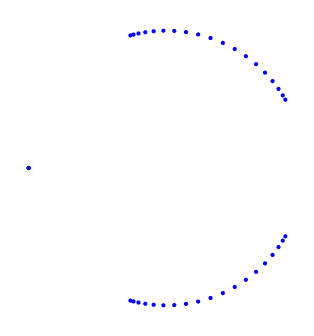

```mathematica
Graphics[{Blue,pp1}]
```

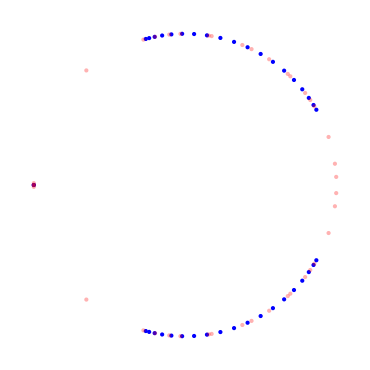

```mathematica
Show[Graphics[{Blue,pp1}],Graphics[{PointSize[Large],Opacity[0.3],Red,pp2}]]
```

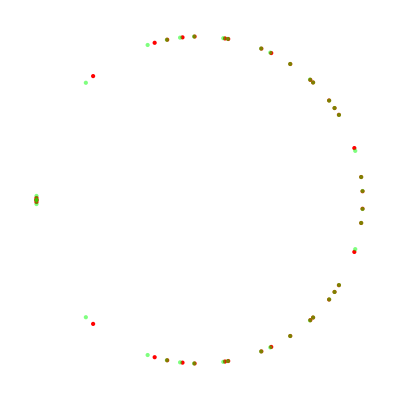

```mathematica
Show[Graphics[{Red,pp2}],Graphics[{PointSize[Large],Opacity[0.5],Green,pp3}]]
```

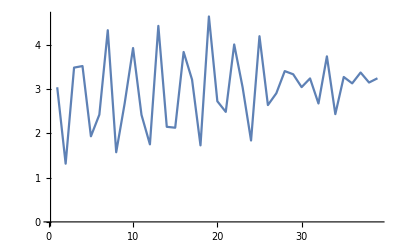

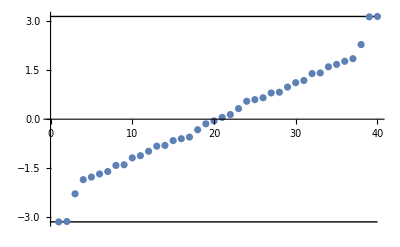

0.0000212159

```mathematica
q=bnFig5a;
ListPlot[q, PlotRange -> All, Joined -> True] 
Show[Plot[{π,-π},{x,0,40},PlotStyle->{{Black,Thin},{Black,Thin}}],ListPlot[Eigen[q]]]
Min[Abs[Eigen[q]-π],Abs[Eigen[q]π]]
```

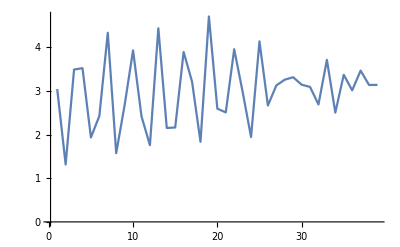

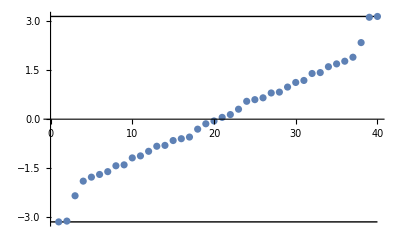

0.000016032

```mathematica
q=bnFig5b;
ListPlot[q, PlotRange -> All, Joined -> True] 
Show[Plot[{π,-π},{x,0,40},PlotStyle->{{Black,Thin},{Black,Thin}}],ListPlot[Eigen[q]]]
Min[Abs[Eigen[q]-π],Abs[Eigen[q]π]]
```

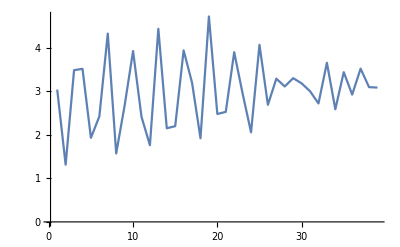

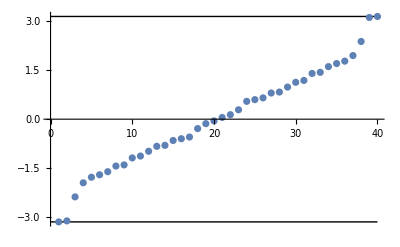

0.0000182925

```mathematica
q=bnFig5c;
ListPlot[q, PlotRange -> All, Joined -> True] 
Show[Plot[{π,-π},{x,0,40},PlotStyle->{{Black,Thin},{Black,Thin}}],ListPlot[Eigen[q]]]
Min[Abs[Eigen[q]-π],Abs[Eigen[q]π]]
```

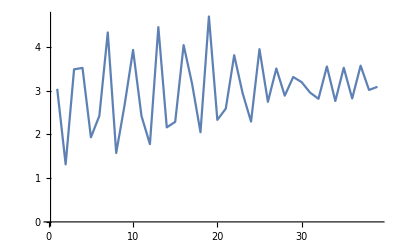

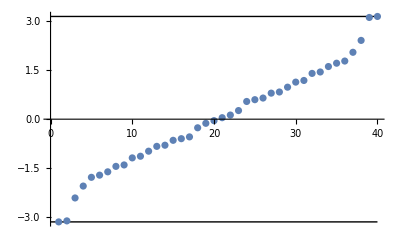

0.0000312846

```mathematica
q=bnFig5d;
ListPlot[q, PlotRange -> All, Joined -> True] 
Show[Plot[{π,-π},{x,0,40},PlotStyle->{{Black,Thin},{Black,Thin}}],ListPlot[Eigen[q]]]
Min[Abs[Eigen[q]-π],Abs[Eigen[q]π]]
```

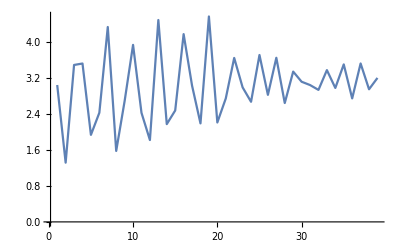

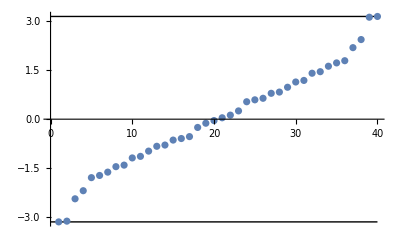

0.0000910336

```mathematica
q=bnFig5e;
ListPlot[q, PlotRange -> All, Joined -> True] 
Show[Plot[{π,-π},{x,0,40},PlotStyle->{{Black,Thin},{Black,Thin}}],ListPlot[Eigen[q]]]
Min[Abs[Eigen[q]-π],Abs[Eigen[q]π]]
```

```mathematica
Abs[1/40∑_(k=1)^Length[bnFig5g] bnFig5g[[k]] ⅇ^(ⅈ k 2π/2)]
```

0.285165

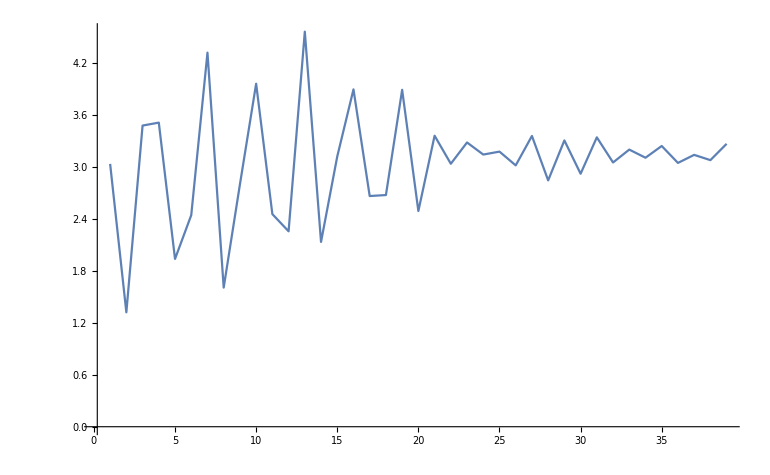

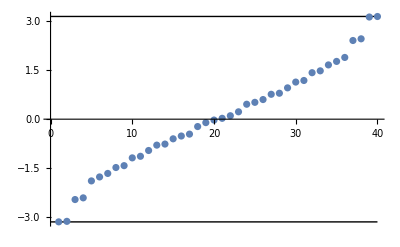

0.00125849

```mathematica
q=bnFig5g;
ListPlot[q, PlotRange -> All, Joined -> True] 
Show[Plot[{π,-π},{x,0,40},PlotStyle->{{Black,Thin},{Black,Thin}}],ListPlot[Eigen[q]]]
Min[Abs[Eigen[q]-π],Abs[Eigen[q]π]]
```

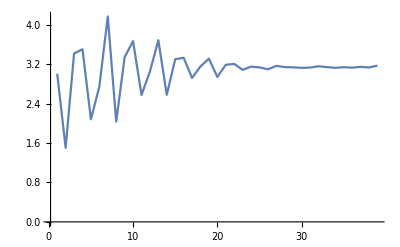

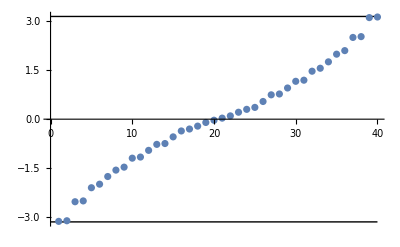

0.0165001

```mathematica
q=bnFig5h;
ListPlot[q, PlotRange -> All, Joined -> True] 
Show[Plot[{π,-π},{x,0,40},PlotStyle->{{Black,Thin},{Black,Thin}}],ListPlot[Eigen[q]]]
Min[Abs[Eigen[q]-π],Abs[Eigen[q]π]]
```

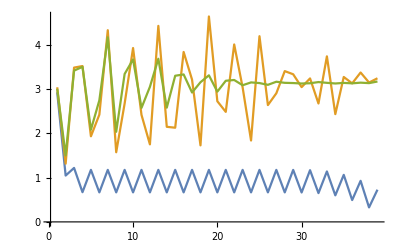

```mathematica
ListPlot[{bnFig4,bnFig5a,bnFig5h}, PlotRange -> All, Joined -> True]
```

```mathematica
Show[Plot[{π,-π},{x,0,40},PlotStyle->{{Black,Thin},{Black,Thin}}],ListPlot[Eigen[q]]]
```

-Graphics-

## Analysis

```mathematica
Eigenvalues[Ham[bnFig4]]
```

{3.14198,-3.14198,1.8336,-1.8336,-1.81063,1.81063,-1.77335,1.77335,-1.72315,1.72315,-1.66162,1.66162,1.59047,-1.59047,1.51136,-1.51136,-1.42585,1.42585,1.33541,-1.33541,-1.24141,1.24141,1.14518,-1.14518,1.04807,-1.04807,0.951556,-0.951556,-0.857377,0.857377,-0.767682,0.767682,-0.685243,0.685243,-0.613645,0.613645,0.557273,-0.557273,-0.520837,0.520837}

```mathematica
Eigensystem[Ham[bnFig4]][[2]][[2]]
```

{-0.65024,0.697886,-0.27636,0.113263,-0.0283716,0.0112034,-0.0027886,0.00110078,-0.000273976,0.00010815,-0.0000269176,0.0000106255,-2.6446×10^-6,1.04393×10^-6,-2.59827×10^-7,1.02565×10^-7,-2.55275×10^-8,1.00768×10^-8,-2.50803×10^-9,9.90023×10^-10,-2.46409×10^-10,9.72678×10^-11,-2.42092×10^-11,9.55637×10^-12,-2.3785×10^-12,9.38884×10^-13,-2.33668×10^-13,9.22276×10^-14,-2.29385×10^-14,9.0434×10^-15,-2.23664×10^-15,8.74838×10^-16,-2.09791×10^-16,7.93628×10^-17,-1.71673×10^-17,5.96539×10^-18,-1.02688×10^-18,3.06633×10^-19,-3.37361×10^-20,7.80882×10^-21}

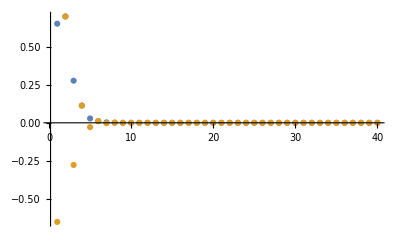

```mathematica
ListPlot[{Eigensystem[Ham[bnFig4]][[2]][[1]],Eigensystem[Ham[bnFig4]][[2]][[2]]},PlotRange->All]
```

```mathematica
(Eigenvalues[Ham[bnFig5a]])
```

{6.2296,-6.2296,6.14212,-6.14212,-5.95998,5.95998,-5.7355,5.7355,-5.62889,5.62889,-5.48126,5.48126,5.30131,-5.30131,-5.10036,5.10036,4.88856,-4.88856,-4.6816,4.6816,-4.51242,4.51242,4.00125,-4.00125,-3.14161,3.14161,3.12923,-3.12923,-1.84994,1.84994,-1.67585,1.67585,-1.4146,1.4146,-1.11639,1.11639,0.825224,-0.825224,0.597077,-0.597077}

```mathematica
Eigensystem[Ham[bnFig5a]][[1]][[26]]
```

-3.14161

```mathematica
Eigensystem[Ham[bnFig5a]][[2]][[26]]
```

{-0.649631,0.67134,-0.102098,-0.161192,0.244978,-0.104671,-0.0597601,0.101923,-0.0390912,-0.0140357,0.0378344,-0.026368,-0.00493157,0.0139305,-0.0102127,0.00101879,0.00482656,-0.00593591,0.00181707,0.000980621,-0.00422423,0.00426555,-0.000724892,-0.00487559,0.00953187,-0.00500339,-0.00919476,0.0144886,-0.00552341,-0.00959372,0.0159538,-0.00645735,-0.0117458,0.0144879,-0.000657908,-0.0101426,0.0108723,-0.000717919,-0.0109366,0.0112905}

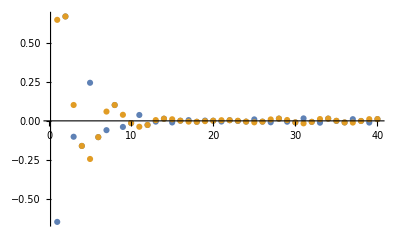

```mathematica
ListPlot[{Eigensystem[Ham[bnFig5a]][[2]][[26]],Eigensystem[Ham[bnFig5a]][[2]][[25]]},PlotRange->All]
```

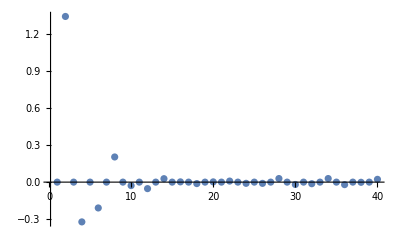

```mathematica
ListPlot[Eigensystem[Ham[bnFig5a]][[2]][[26]]+Eigensystem[Ham[bnFig5a]][[2]][[25]],PlotRange->All]
```

```mathematica
(*Edge modes*)
Ev:= Pi
s:= bnFig4
w1:={1, Ev/s[[1]]}
For[n=2,n<10,n++, w1= Append[w1, (Ev w1[[n]]-s[[n-1]]*w1[[n-1]])/s[[n]]]; Print[w1]]
```

{1,1.07314,0.424227}

{1,1.07314,0.424227,0.172141}

{1,1.07314,0.424227,0.172141,0.0353769}

{1,1.07314,0.424227,0.172141,0.0353769,-0.00368584}

{1,1.07314,0.424227,0.172141,0.0353769,-0.00368584,-0.0797348}

{1,1.07314,0.424227,0.172141,0.0353769,-0.00368584,-0.0797348,-0.211135}

{1,1.07314,0.424227,0.172141,0.0353769,-0.00368584,-0.0797348,-0.211135,-0.854537}

{1,1.07314,0.424227,0.172141,0.0353769,-0.00368584,-0.0797348,-0.211135,-0.854537,-2.1654}

```mathematica
Pi/s[[1]]
(Pi^2/(s[[1]]*s[[2]]))(1-(s[[1]]/Ev)^2)
(Pi^3/(s[[1]]*s[[2]]*s[[3]]))(1-(s[[1]]/Ev)^2-(s[[2]]/Ev)^2)
(Pi^4/(s[[1]]*s[[2]]*s[[3]]*s[[4]]))(1-(1/Ev^2)(s[[1]]^2+ s[[2]]^2+s[[3]]^2)+ s[[1]]^2 s[[3]]^2/Ev^4)
(Pi^5/(s[[1]]*s[[2]]*s[[3]]*s[[4]]*s[[5]]))(1-(1/Ev^2)(s[[1]]^2+ s[[2]]^2+s[[3]]^2+s[[4]]^2)+ (s[[1]]^2 s[[3]]^2+s[[1]]^2 s[[4]]^2+s[[2]]^2 s[[4]]^2)/Ev^4)
(Pi^6/(s[[1]]*s[[2]]*s[[3]]*s[[4]]*s[[5]]*s[[6]]))(1-(1/Ev^2)(s[[1]]^2+ s[[2]]^2+s[[3]]^2+s[[4]]^2+s[[5]]^2)+ (s[[1]]^2 s[[3]]^2+s[[1]]^2 s[[4]]^2+s[[1]]^2 s[[5]]^2+s[[2]]^2 s[[4]]^2+s[[2]]^2 s[[5]]^2+s[[3]]^2 s[[5]]^2)/Ev^4- s[[1]]^2 s[[3]]^2 s[[5]]^2/Ev^6)
```

1.07314

0.424227

0.172141

0.0353769

-0.00368584

-0.0797348

```mathematica
Ev:= Pi
sa:= bnFig5a
w1a:={1, Ev/s[[1]]}
For[n=2,n<10,n++, w1a= Append[w1a, (Ev w1a[[n]]-sa[[n-1]]*w1a[[n-1]])/sa[[n]]]; Print[w1a]]
```

{1,1.07314,0.252096}

{1,1.07314,0.252096,-0.177522}

{1,1.07314,0.252096,-0.177522,-0.408064}

{1,1.07314,0.252096,-0.177522,-0.408064,-0.339979}

{1,1.07314,0.252096,-0.177522,-0.408064,-0.339979,-0.115301}

{1,1.07314,0.252096,-0.177522,-0.408064,-0.339979,-0.115301,0.106523}

{1,1.07314,0.252096,-0.177522,-0.408064,-0.339979,-0.115301,0.106523,0.530107}

{1,1.07314,0.252096,-0.177522,-0.408064,-0.339979,-0.115301,0.106523,0.530107,0.560529}

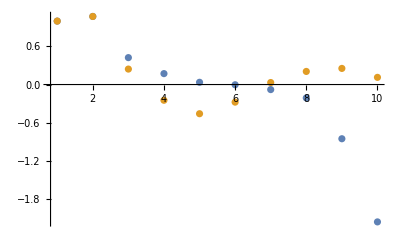

```mathematica
ListPlot[{w1,w1a}, PlotRange -> All]
```

```mathematica
s:=bnFig4
Htest := {{0,s[[1]],0,0,0,0},{s[[1]],0,s[[2]],0,0,0},{0,s[[2]],0,s[[3]],0,0},{0,0,s[[3]],0,s[[4]],0},{0,0,0,s[[4]],0,s[[5]]},{0,0,0,0,s[[5]],0}}
Htest2 := {{0,s[[1]],0,0},{s[[1]],0,s[[2]],0},{0,s[[2]],0,s[[3]]},{0,0,s[[3]],0}}
```

```mathematica
Eigenvalues[Htest]
Eigenvalues[Htest2]
```

{-3.14196,3.14196,-1.53384,1.53384,0.87009,-0.87009}

{-3.13995,3.13995,1.13636,-1.13636}

```mathematica
N[Pi]
```

3.14159

```mathematica
MovingAverage[{a,b,c,d,e},3]
```

{1/3 (a+b+c),1/3 (b+c+d),1/3 (c+d+e)}

```mathematica
{MovingAverage[Abs[Differences[bnFig4]],m],MovingAverage[Abs[Differences[shbnFig5a]],m],MovingAverage[Abs[Differences[shbnFig5b]],m],MovingAverage[Abs[Differences[shbnFig5c]],m],MovingAverage[Abs[Differences[shbnFig5d]],m],MovingAverage[Abs[Differences[shbnFig5e]],m],MovingAverage[Abs[Differences[shbnFig5f]],m],MovingAverage[Abs[Differences[shbnFig5g]],m],MovingAverage[Abs[Differences[shbnFig5h]],m]}
```

{{0.776486,0.433357,0.517283,0.507319,0.508269,0.508177,0.508186,0.508185,0.508185,0.508185,0.508185,0.508185,0.508185,0.508185,0.508185,0.508185,0.508185,0.508185,0.508185,0.508185,0.508185,0.508188,0.508175,0.50822,0.508077,0.508492,0.507427,0.509807,0.505261,0.512722,0.502374,0.515178,0.501391,0.516539,0.500945},{0.77631,0.432449,0.523997,0.457831,0.650297,0.62649,0.551088,0.671302,0.495869,0.492588,0.563369,0.482791,0.458396,0.658427,0.799039,0.859519,0.832062,0.652772,0.508726,0.403523,0.357967,0.377623,0.36907,0.392398,0.376117,0.285062,0.217084,0.174737,0.164566,0.12859,0.109441,0.0843008,0.102545,0.139001,0.112947},{0.776331,0.43202,0.526972,0.443523,0.638431,0.670612,0.578496,0.690172,0.526319,0.46924,0.537252,0.484813,0.444567,0.633664,0.79568,0.882199,0.864363,0.681935,0.537481,0.420152,0.356769,0.365445,0.349907,0.350493,0.331502,0.25874,0.203474,0.154745,0.147258,0.12632,0.0994391,0.0887895,0.118927,0.141429,0.112137},{0.776355,0.431501,0.530461,0.42983,0.617714,0.694155,0.580204,0.688492,0.540266,0.450559,0.523265,0.483031,0.4379,0.613785,0.788317,0.901937,0.888739,0.699627,0.554889,0.430211,0.354512,0.352335,0.331633,0.319522,0.292455,0.24192,0.194052,0.141711,0.138759,0.125073,0.0986987,0.0926928,0.133738,0.143052,0.111439},{0.776417,0.430176,0.538965,0.406128,0.561532,0.697442,0.555253,0.665058,0.550797,0.432858,0.513161,0.477785,0.440439,0.590908,0.769975,0.930641,0.921365,0.717494,0.571842,0.437031,0.344318,0.321661,0.289531,0.26511,0.24628,0.234042,0.201058,0.149607,0.149649,0.144145,0.121865,0.110755,0.150872,0.141384,0.109118},{0.77659,0.426515,0.559119,0.460284,0.526735,0.701071,0.595134,0.639079,0.583274,0.467822,0.491252,0.449329,0.454138,0.574982,0.740368,0.958829,0.950363,0.73149,0.582849,0.425554,0.306164,0.255709,0.20536,0.168874,0.175684,0.202214,0.192036,0.169338,0.173259,0.172919,0.149281,0.108232,0.135743,0.119677,0.0986605},{0.77594,0.425893,0.542674,0.420076,0.523689,0.595134,0.514436,0.609109,0.438597,0.434939,0.444466,0.349822,0.465634,0.569057,0.720641,0.987702,0.954835,0.739462,0.591101,0.399344,0.264115,0.200845,0.131068,0.0944724,0.100481,0.133453,0.152883,0.156202,0.177281,0.182901,0.154112,0.105356,0.121777,0.111933,0.10644},{0.777729,0.389289,0.609617,0.521052,0.397223,0.477393,0.350899,0.432784,0.459985,0.432041,0.349044,0.223701,0.367203,0.456867,0.641531,0.950835,0.916621,0.778126,0.615445,0.402631,0.261463,0.214904,0.159698,0.103456,0.102754,0.106975,0.131613,0.160589,0.203535,0.189648,0.154735,0.0874104,0.0805523,0.0891055,0.086397},{0.675081,0.297556,0.358631,0.297713,0.22703,0.216002,0.149219,0.178067,0.148387,0.167649,0.173983,0.168671,0.242847,0.38121,0.620062,0.84919,0.908655,0.849033,0.616972,0.439607,0.348809,0.273243,0.250002,0.231884,0.209376,0.216393,0.326106,0.241064,0.22062,0.202942,0.111481,0.126318,0.0925916,0.0787762,0.0587671}}